```mathematica
Clear[ω0,γ,F0,α];
sol=(F0*Exp[-γ*t])/(√(ω0^2-γ^2))Integrate[Exp[-α*tp]Exp[+γ*tp]Sin[√(ω0^2-γ^2)(t-tp)],{tp,0,t}]
```

(ⅇ^(-t γ) F0 (ⅇ^(t (-α+γ)) √(-γ^2+ω0^2)-√(-γ^2+ω0^2) Cos[t √(-γ^2+ω0^2)]+(α-γ) Sin[t √(-γ^2+ω0^2)]))/((α^2-2 α γ+ω0^2) √(-γ^2+ω0^2))

```mathematica
sol/.t->0
```

0

```mathematica
D[sol,t]/.t->0//Simplify
```

0

```mathematica
Simplify[Limit[sol,γ->0],Subscript[ω, 0]>0]
```

(F0 (α Sin[t ω_0]+(ⅇ^(-t α)-Cos[t ω_0]) ω_0))/(ω_0 (α^2+ω_0^2))

```mathematica
ω0=2;
γ=0.1;
F0=1;
α=1;
```

```mathematica
numSol=NDSolve[{x''[t]+2γ*x'[t]+ω0^2*x[t]==F0*Exp[-α*t],x[0]==0,x'[0]==0},x,{t,0,10}]
```

{{x→InterpolatingFunction[…]}}

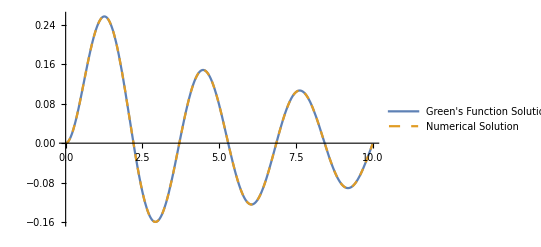

```mathematica
Plot[{sol,Evaluate[x[t]]/.numSol},{t,0,10},PlotStyle->{Thick,Dashed},PlotLegends->{"Green's Function Solution", "Numerical Solution"}]
```